# Fitting of Build up and Relaxation time (20120516)

```mathematica
bg=24.4;
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 415.006 | 134.776 | 3.07924 | 0.0116558
t | 5.75069 | 2.54155 | 2.26267 | 0.0471543

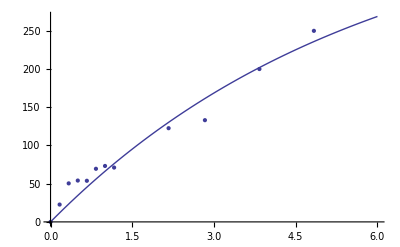

```mathematica
Build={
{0,0},
{10/60,47.1-bg},
{20/60,74.8-bg},
{30/60,78.5-bg},
{40/60,78.2-bg},
{50/60, 93.9-bg},
{60/60, 97.6-bg},
{70/60, 95.5-bg},
{130/60, 147.0-bg},
{170/60, 157.5-bg},
{230/60, 200},
{290/60, 250}};
BFit=NonlinearModelFit[Build,a(1-Exp[-x/t]),{a,t},x];
BFit["ParameterTable"]
Show[
Plot[BFit[x],{x,0,6},PlotRange->{0, All}],
ListPlot[Build,PlotRange->{{0,3.5},{0, All}}]]
```

```mathematica
42.577*0.2 10^-3
```

0.0085154

```mathematica
1/2.6
```

0.384615